```mathematica
K[tp_] = {{0, -λ*(T-tp)}, {-r*K1[tp], K1[tp]}}
```

{{0,-(T-tp) λ},{-r K1[tp],K1[tp]}}

```mathematica
B[tp_] = {{σg, 0}, {0, K1'[tp]*σξ}}
```

{{σg,0},{0,σξ K1'[tp]}}

```mathematica
s0 = {{x0, xx0},{xx0, xh0}}
```

{{x0,xx0},{xx0,xh0}}

```mathematica
FullSimplify[((MatrixExp[K[0]].s0).MatrixExp[Transpose[K[0]]])[[1,1]]]
```

1/(K1[0] (4 r T λ+K1[0]))ⅇ^K1[0] (-2 T λ (T xh0 λ+(-r x0+xx0) K1[0])+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T^2 xh0 λ^2+2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2)-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])

```mathematica
Expand[Series[%312/.K1[0]->λ*T/ep, {ep, 0, 1}]]
```

ⅇ^((T λ)/ep+O[ep]^2) Cosh[(T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^(3/2)] (x0+O[ep]^1)+ⅇ^((T λ)/ep+O[ep]^2) (-2 (-r x0+xx0) ep+O[ep]^2)+ⅇ^((T λ)/ep+O[ep]^2) (-x0+O[ep]^1) Sinh[(T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^2]

```mathematica
c
```

```mathematica
Normal@%
```

ⅇ^((T λ)/ep) (-2 ep (-r x0+xx0)+x0 Cosh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]-x0 Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ])

```mathematica
%323/.ep->λ*T/K1[0]
```

ⅇ^K1[0] (x0 Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-(2 T (-r x0+xx0) λ)/K1[0]-x0 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])

```mathematica
ⅇ^K1[0] (x0 Cosh[2 r T λ+K1[0]]-x0 Sinh[2 r T λ+K1[0]])
```

ⅇ^K1[0] (x0 Cosh[2 r T λ+K1[0]]-x0 Sinh[2 r T λ+K1[0]])

```mathematica
FullSimplify[(2 ⅇ^(-2 r T λ) (-1+ⅇ^(λ (2 r T-K1[0]/T)))^2 T^4 σξ^2 K1'[0])/K1[0]^2]
```

(2 ⅇ^(-2 r T λ) (-1+ⅇ^(2 r T λ-(λ K1[0])/T))^2 T^4 σξ^2 K1'[0])/K1[0]^2

```mathematica
Solve[ⅇ^K1[0] (x0 Cosh[2 r T λ+K1[0]]-x0 Sinh[2 r T λ+K1[0]])==(2 ⅇ^(-2 r T λ) (-1+ⅇ^(λ (2 r T-K1[0]/T)))^2 T^4 σξ^2 K1'[0])/K1[0]^2, K1[0]]
```

Solve[ⅇ^K1[0] (x0 Cosh[2 r T λ+K1[0]]-x0 Sinh[2 r T λ+K1[0]])==(2 ⅇ^(-2 r T λ) (-1+ⅇ^(λ (2 r T-K1[0]/T)))^2 T^4 σξ^2 K1'[0])/K1[0]^2,K1[0]]

```mathematica
L[K1[tp], K1'[tp], tp] = FullSimplify[(MatrixExp[K[tp]].B[tp].Transpose[B[tp]].MatrixExp[Transpose[K[tp]]])[[1,1]]]
```

(ⅇ^(K1[tp]-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2))/(2 K1[tp] (4 r (T-tp) λ+K1[tp]))

```mathematica
%252/. K1[tp]->λ(tp-T)/ep
```

(ⅇ^(((-T+tp) λ)/ep-√(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep)) ep ((2 (1+ⅇ^(√(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep)))^2 r (T-tp) (-T+tp) λ^2 σg^2)/ep+((1+ⅇ^(2 √(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep))) (-T+tp)^2 λ^2 σg^2)/ep^2-(-1+ⅇ^(2 √(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep))) (((-T+tp) λ)/ep)^(3/2) √(4 r (T-tp) λ+((-T+tp) λ)/ep) σg^2+2 (-1+ⅇ^(√(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep)))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2))/(2 (-T+tp) λ (4 r (T-tp) λ+((-T+tp) λ)/ep))

```mathematica
Series[%255, {ep, 0,3}]
```

((ⅇ^(-2 r (T-tp) λ) ep^2)/(2 λ^2)+(ⅇ^(-2 r (T-tp) λ) r (T-tp) (-2+r T λ-r tp λ) ep^3)/λ^2+O[ep]^(7/2)) ((1+ⅇ^((2 λ)/ep+4 r (T-tp) λ-4 (r^2 (T-tp)^2 λ) ep+8 r^3 (T-tp)^3 λ ep^2-20 (r^4 (T-tp)^4 λ) ep^3+O[ep]^(7/2))) ((λ^2 σg^2)/ep^2+O[ep]^4)+(1+ⅇ^(λ/ep+2 r (T-tp) λ-2 (r^2 (T-tp)^2 λ) ep+4 r^3 (T-tp)^3 λ ep^2-10 (r^4 (T-tp)^4 λ) ep^3+O[ep]^(7/2)))^2 ((2 r (T-tp) λ^2 σg^2)/ep+O[ep]^4)+ⅇ^((2 λ)/ep+4 r (T-tp) λ-4 (r^2 (T-tp)^2 λ) ep+O[ep]^2) (-(λ^2 σg^2)/ep^2-(2 (r (T-tp) λ^2 σg^2))/ep+2 r^2 (T-tp)^2 λ^2 σg^2-4 (r^3 (T-tp)^3 λ^2 σg^2) ep+O[ep]^2)+((λ^2 σg^2)/ep^2+(2 r (T-tp) λ^2 σg^2)/ep-2 (r^2 (T-tp)^2 λ^2 σg^2)+4 r^3 (T-tp)^3 λ^2 σg^2 ep+O[ep]^2)+2 (-1+ⅇ^(λ/ep+2 r (T-tp) λ-2 (r^2 (T-tp)^2 λ) ep+4 r^3 (T-tp)^3 λ ep^2-10 (r^4 (T-tp)^4 λ) ep^3+O[ep]^(7/2)))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)

```mathematica
Normal@Simplify[((1+ⅇ^((2 λ)/ep+4 r (T-tp) λ-4 (r^2 (T-tp)^2 λ) ep+8 r^3 (T-tp)^3 λ ep^2-20 (r^4 (T-tp)^4 λ) ep^3+O[ep]^(7/2))) ((λ^2 σg^2)/ep^2+O[ep]^4)+(1+ⅇ^(λ/ep+2 r (T-tp) λ-2 (r^2 (T-tp)^2 λ) ep+4 r^3 (T-tp)^3 λ ep^2-10 (r^4 (T-tp)^4 λ) ep^3+O[ep]^(7/2)))^2 ((2 r (T-tp) λ^2 σg^2)/ep+O[ep]^4)+ⅇ^((2 λ)/ep+4 r (T-tp) λ-4 (r^2 (T-tp)^2 λ) ep+O[ep]^2) (-(λ^2 σg^2)/ep^2-(2 (r (T-tp) λ^2 σg^2))/ep+2 r^2 (T-tp)^2 λ^2 σg^2-4 (r^3 (T-tp)^3 λ^2 σg^2) ep+O[ep]^2)+((λ^2 σg^2)/ep^2+(2 r (T-tp) λ^2 σg^2)/ep-2 (r^2 (T-tp)^2 λ^2 σg^2)+4 r^3 (T-tp)^3 λ^2 σg^2 ep+O[ep]^2)+2 (-1+ⅇ^(λ/ep+2 r (T-tp) λ-2 (r^2 (T-tp)^2 λ) ep+4 r^3 (T-tp)^3 λ ep^2-10 (r^4 (T-tp)^4 λ) ep^3+O[ep]^(7/2)))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)]
```

(λ^2 σg^2)/ep^2+((1+ⅇ^((2 λ)/ep+4 r (T-tp) λ-4 ep r^2 (T-tp)^2 λ+8 ep^2 r^3 (T-tp)^3 λ-20 ep^3 r^4 (T-tp)^4 λ)) λ^2 σg^2)/ep^2+(2 r (T-tp) λ^2 σg^2)/ep+(2 (1+ⅇ^(λ/ep+2 r (T-tp) λ-2 ep r^2 (T-tp)^2 λ+4 ep^2 r^3 (T-tp)^3 λ-10 ep^3 r^4 (T-tp)^4 λ))^2 r (T-tp) λ^2 σg^2)/ep-2 r^2 (T-tp)^2 λ^2 σg^2+4 ep r^3 (T-tp)^3 λ^2 σg^2+ⅇ^((2 λ)/ep+4 r (T-tp) λ-4 ep r^2 (T-tp)^2 λ) (-(λ^2 σg^2)/ep^2-(2 r (T-tp) λ^2 σg^2)/ep+2 r^2 (T-tp)^2 λ^2 σg^2-4 ep r^3 (T-tp)^3 λ^2 σg^2)+2 (-1+ⅇ^(λ/ep+2 r (T-tp) λ-2 ep r^2 (T-tp)^2 λ+4 ep^2 r^3 (T-tp)^3 λ-10 ep^3 r^4 (T-tp)^4 λ))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2

```mathematica
(λ^2 σg^2)/ep^2+((1+ⅇ^((2 λ)/ep+4 r (T-tp) λ)) λ^2 σg^2)/ep^2+(2 r (T-tp) λ^2 σg^2)/ep+(2 (1+ⅇ^(λ/ep+2 r (T-tp) λ))^2 r (T-tp) λ^2 σg^2)/ep-2 r^2 (T-tp)^2 λ^2 σg^2+4 ep r^3 (T-tp)^3 λ^2 σg^2+ⅇ^((2 λ)/ep+4 r (T-tp) λ) (-(λ^2 σg^2)/ep^2-(2 r (T-tp) λ^2 σg^2)/ep+2 r^2 (T-tp)^2 λ^2 σg^2-4 ep r^3 (T-tp)^3 λ^2 σg^2)+2 (-1+ⅇ^(λ/ep+2 r (T-tp) λ))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2
```

(λ^2 σg^2)/ep^2+((1+ⅇ^((2 λ)/ep+4 r (T-tp) λ)) λ^2 σg^2)/ep^2+(2 r (T-tp) λ^2 σg^2)/ep+(2 (1+ⅇ^(λ/ep+2 r (T-tp) λ))^2 r (T-tp) λ^2 σg^2)/ep-2 r^2 (T-tp)^2 λ^2 σg^2+4 ep r^3 (T-tp)^3 λ^2 σg^2+ⅇ^((2 λ)/ep+4 r (T-tp) λ) (-(λ^2 σg^2)/ep^2-(2 r (T-tp) λ^2 σg^2)/ep+2 r^2 (T-tp)^2 λ^2 σg^2-4 ep r^3 (T-tp)^3 λ^2 σg^2)+2 (-1+ⅇ^(λ/ep+2 r (T-tp) λ))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2

```mathematica
%*(ⅇ^(-2 r (T-tp) λ) ep^2)/(2 λ^2)
```

1/(2 λ^2)ⅇ^(-2 r (T-tp) λ) ep^2 ((λ^2 σg^2)/ep^2+((1+ⅇ^((2 λ)/ep+4 r (T-tp) λ)) λ^2 σg^2)/ep^2+(2 r (T-tp) λ^2 σg^2)/ep+(2 (1+ⅇ^(λ/ep+2 r (T-tp) λ))^2 r (T-tp) λ^2 σg^2)/ep-2 r^2 (T-tp)^2 λ^2 σg^2+4 ep r^3 (T-tp)^3 λ^2 σg^2+ⅇ^((2 λ)/ep+4 r (T-tp) λ) (-(λ^2 σg^2)/ep^2-(2 r (T-tp) λ^2 σg^2)/ep+2 r^2 (T-tp)^2 λ^2 σg^2-4 ep r^3 (T-tp)^3 λ^2 σg^2)+2 (-1+ⅇ^(λ/ep+2 r (T-tp) λ))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)

```mathematica
Cancel[%330]
```

ⅇ^(-2 r (T-tp) λ) (σg^2+2 ep r T σg^2+2 ⅇ^(λ/ep+2 r (T-tp) λ) ep r T σg^2-ep^2 r^2 T^2 σg^2+ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^2 r^2 T^2 σg^2+2 ep^3 r^3 T^3 σg^2-2 ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^3 r^3 T^3 σg^2-2 ep r tp σg^2-2 ⅇ^(λ/ep+2 r (T-tp) λ) ep r tp σg^2+2 ep^2 r^2 T tp σg^2-2 ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^2 r^2 T tp σg^2-6 ep^3 r^3 T^2 tp σg^2+6 ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^3 r^3 T^2 tp σg^2-ep^2 r^2 tp^2 σg^2+ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^2 r^2 tp^2 σg^2+6 ep^3 r^3 T tp^2 σg^2-6 ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^3 r^3 T tp^2 σg^2-2 ep^3 r^3 tp^3 σg^2+2 ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^3 r^3 tp^3 σg^2+ep^2 T^2 σξ^2 K1'[tp]^2-2 ⅇ^(λ/ep+2 r (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2+ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2-2 ep^2 T tp σξ^2 K1'[tp]^2+4 ⅇ^(λ/ep+2 r (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2-2 ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2+ep^2 tp^2 σξ^2 K1'[tp]^2-2 ⅇ^(λ/ep+2 r (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2+ⅇ^((2 λ)/ep+4 r (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2)

```mathematica
Simplify[%]
```

ⅇ^(-2 r (T-tp) λ) ((1+2 (1+ⅇ^((1/ep+2 r (T-tp)) λ)) ep r (T-tp)+(-1+ⅇ^(2 (1/ep+2 r (T-tp)) λ)) ep^2 r^2 (T-tp)^2-2 (-1+ⅇ^(2 (1/ep+2 r (T-tp)) λ)) ep^3 r^3 (T-tp)^3) σg^2+(-1+ⅇ^((1/ep+2 r (T-tp)) λ))^2 ep^2 (T-tp)^2 σξ^2 K1'[tp]^2)

```mathematica
%/.ep->(tp-T)/K1[tp]
```

ⅇ^(-2 r (T-tp) λ) (σg^2 (1-(2 (-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^3 (T-tp)^3 (-T+tp)^3)/K1[tp]^3+((-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 (T-tp)^2 (-T+tp)^2)/K1[tp]^2+(2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp) (-T+tp))/K1[tp])+((-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 (-T+tp)^2 σξ^2 K1'[tp]^2)/K1[tp]^2)

```mathematica
ⅇ^(-2 r (T-tp) λ) (σg^2 (1((-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 (T-tp)^2 (-T+tp)^2)/K1[tp]^2+(2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp) (-T+tp))/K1[tp])+((-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 (-T+tp)^2 σξ^2 K1'[tp]^2)/K1[tp]^2)
```

ⅇ^(-2 r (T-tp) λ) (σg^2 (((-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 (T-tp)^2 (-T+tp)^2)/K1[tp]^2+(2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp) (-T+tp))/K1[tp])+((-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 (-T+tp)^2 σξ^2 K1'[tp]^2)/K1[tp]^2)

```mathematica
FullSimplify[%]
```

1/K1[tp]^2 ⅇ^(2 r (-T+tp) λ) (-r (T-tp)^2 σg^2 (-(-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp)^2+2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) K1[tp])+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^4 σξ^2 K1'[tp]^2)

```mathematica
D[1/K1[tp]^2 ⅇ^(2 r (-T+tp) λ) (-r (T-tp)^2 σg^2 (-(-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp)^2+2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) K1[tp])+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^4 σξ^2 K1'[tp]^2), K1'[tp]]
```

(2 ⅇ^(2 r (-T+tp) λ) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^4 σξ^2 K1'[tp])/K1[tp]^2

```mathematica
%/.tp->0
```

(2 ⅇ^(-2 r T λ) (-1+ⅇ^(λ (2 r T-K1[0]/T)))^2 T^4 σξ^2 K1'[0])/K1[0]^2

```mathematica
EulerEquations[%, K1[tp], tp]
```

1/K1[tp]^3 2 ⅇ^(2 r (-T+tp) λ) (T-tp) (r (T-tp) σg^2 (-(-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp)^2+2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) K1[tp])+4 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 σξ^2 K1[tp] K1'[tp]-2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 r (T-tp)^3 λ σξ^2 K1[tp] K1'[tp]+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^3 σξ^2 K1'[tp]^2+K1[tp] (-r σg^2 ((T-tp) (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r (T-tp) λ)-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) λ K1[tp])-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp)^2 λ σξ^2 K1'[tp]^2)-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) λ σξ^2 K1[tp] K1'[tp] (-K1[tp]-(T-tp) (2 r (T-tp)+K1'[tp]))-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^3 σξ^2 K1[tp] K1''[tp])==0

```mathematica
Simplify[%]
```

1/K1[tp]ⅇ^(2 r (-T+tp) λ) (T-tp) (ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) λ K1[tp]^2 (r σg^2+2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) σξ^2 K1'[tp])-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp)^3 ((1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 σg^2-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) σξ^2 K1'[tp]^2)-(T-tp) K1[tp] (r (-1-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r (T-tp) λ) σg^2-2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) (-2+r T λ-r tp λ+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (2+r (T-tp) λ)) σξ^2 K1'[tp]-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) λ σξ^2 K1'[tp]^2+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 σξ^2 K1''[tp]))==0

```mathematica
Collect[(ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) λ K1[tp]^2 (r σg^2+2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) σξ^2 K1'[tp])-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp)^3 ((1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 σg^2-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) σξ^2 K1'[tp]^2)-(T-tp) K1[tp] (r (-1-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r (T-tp) λ) σg^2-2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) (-2+r T λ-r tp λ+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (2+r (T-tp) λ)) σξ^2 K1'[tp]-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) λ σξ^2 K1'[tp]^2+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 σξ^2 K1''[tp])), {K1[tp], K1'[tp], K1''[tp]}]
```

r^2 T^3 σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^3 σg^2-3 r^2 T^2 tp σg^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^2 tp σg^2+3 r^2 T tp^2 σg^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T tp^2 σg^2-r^2 tp^3 σg^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 tp^3 σg^2+(T^3 σξ^2-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2-3 T^2 tp σξ^2+6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2+3 T tp^2 σξ^2-6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2-tp^3 σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2) K1'[tp]^2+K1[tp]^2 (ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r λ σg^2+(-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T λ σξ^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T λ σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp λ σξ^2) K1'[tp])+K1[tp] (r T σg^2+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T σg^2-r tp σg^2-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r tp σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^2 λ σg^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T tp λ σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 tp^2 λ σg^2+(4 T^2 σξ^2-8 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 σξ^2+4 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 σξ^2-8 T tp σξ^2+16 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp σξ^2-8 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp σξ^2+4 tp^2 σξ^2-8 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 σξ^2+4 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 σξ^2-2 r T^3 λ σξ^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T^3 λ σξ^2+6 r T^2 tp λ σξ^2-6 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T^2 tp λ σξ^2-6 r T tp^2 λ σξ^2+6 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T tp^2 λ σξ^2+2 r tp^3 λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r tp^3 λ σξ^2) K1'[tp]+(-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 λ σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 λ σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp λ σξ^2-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 λ σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 λ σξ^2) K1'[tp]^2+(-T^3 σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2+3 T^2 tp σξ^2-6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2-3 T tp^2 σξ^2+6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2+tp^3 σξ^2-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2) K1''[tp])

```mathematica
%/ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))
```

ⅇ^(-2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) (r^2 T^3 σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^3 σg^2-3 r^2 T^2 tp σg^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^2 tp σg^2+3 r^2 T tp^2 σg^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T tp^2 σg^2-r^2 tp^3 σg^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 tp^3 σg^2+(T^3 σξ^2-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2-3 T^2 tp σξ^2+6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2+3 T tp^2 σξ^2-6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2-tp^3 σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2) K1'[tp]^2+K1[tp]^2 (ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r λ σg^2+(-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T λ σξ^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T λ σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp λ σξ^2) K1'[tp])+K1[tp] (r T σg^2+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T σg^2-r tp σg^2-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r tp σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^2 λ σg^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T tp λ σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 tp^2 λ σg^2+(4 T^2 σξ^2-8 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 σξ^2+4 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 σξ^2-8 T tp σξ^2+16 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp σξ^2-8 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp σξ^2+4 tp^2 σξ^2-8 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 σξ^2+4 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 σξ^2-2 r T^3 λ σξ^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T^3 λ σξ^2+6 r T^2 tp λ σξ^2-6 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T^2 tp λ σξ^2-6 r T tp^2 λ σξ^2+6 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T tp^2 λ σξ^2+2 r tp^3 λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r tp^3 λ σξ^2) K1'[tp]+(-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 λ σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 λ σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp λ σξ^2-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 λ σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 λ σξ^2) K1'[tp]^2+(-T^3 σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2+3 T^2 tp σξ^2-6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2-3 T tp^2 σξ^2+6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2+tp^3 σξ^2-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2) K1''[tp]))

```mathematica
Simplify[%]
```

ⅇ^(-2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) (ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) λ K1[tp]^2 (r σg^2+2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) σξ^2 K1'[tp])-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp)^3 ((1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 σg^2-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) σξ^2 K1'[tp]^2)-(T-tp) K1[tp] (r (-1-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r (T-tp) λ) σg^2-2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) (-2+r T λ-r tp λ+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (2+r (T-tp) λ)) σξ^2 K1'[tp]-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) λ σξ^2 K1'[tp]^2+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 σξ^2 K1''[tp]))

```mathematica
Simplify[%337]
```

1/K1[tp]^3 ⅇ^(-2 r (T-tp) λ) (-σg^2 (-2 (-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^3 (T-tp)^6-(-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 (T-tp)^4 K1[tp]+2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp)^2 K1[tp]^2-K1[tp]^3)+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^4 σξ^2 K1[tp] K1'[tp]^2)

```mathematica
EulerEquations[%, K1[tp],tp]
```

-1/K1[tp]^3 2 ⅇ^(2 r (T-tp) λ) (ⅇ^(2 r (-T+tp) λ)-ⅇ^(K1[tp]/(-T+tp))) (T-tp)^2 λ^2 σξ^2 (2 ⅇ^(K1[tp]/(-T+tp)) K1[tp]^2 K1'[tp]-(ⅇ^(2 r (-T+tp) λ)-ⅇ^(K1[tp]/(-T+tp))) (T-tp)^2 K1'[tp]^2+(T-tp) K1[tp] (2 (ⅇ^(2 r (-T+tp) λ) (-2+r (T-tp) λ)+ⅇ^(K1[tp]/(-T+tp)) (2+r (T-tp) λ)) K1'[tp]+ⅇ^(K1[tp]/(-T+tp)) K1'[tp]^2+(ⅇ^(2 r (-T+tp) λ)-ⅇ^(K1[tp]/(-T+tp))) (T-tp) K1''[tp]))==0

```mathematica
FullSimplify[%]
```

1/K1[tp]ⅇ^(r (-T+tp) λ) (-1+ⅇ^(2 r (T-tp) λ+K1[tp]/(-T+tp))) (T-tp) λ σξ ((T-tp) ((-T+tp) K1'[tp]^2+K1[tp] (2 (-2+r (T-tp) λ) K1'[tp]+(T-tp) K1''[tp]))+ⅇ^(2 r (T-tp) λ+K1[tp]/(-T+tp)) (2 K1[tp]^2 K1'[tp]+(T-tp)^2 K1'[tp]^2+(T-tp) K1[tp] (K1'[tp] (4+2 r (T-tp) λ+K1'[tp])+(-T+tp) K1''[tp])))==0

```mathematica
FullSimplify[D[%285, K1'[tp]]/.tp->0]
```

1/K1[0]ⅇ^(-2 r T λ-K1[0]/T) (-ⅇ^(2 r T λ)+ⅇ^(K1[0]/T)) T λ σξ (ⅇ^(K1[0]/T) T ((-2+r T λ) K1[0]-T K1'[0])+ⅇ^(2 r T λ) (K1[0] (T (2+r T λ)+K1[0])+T (T+K1[0]) K1'[0]))==0

```mathematica
Solve[-%+ⅇ^K1[0] (x0 Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-x0 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])==0, K1[0]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(1/K1[0]ⅇ^(-2 r T λ-K1[0]/T) (-ⅇ^(2 r T λ)+ⅇ^(K1[0]/T)) T λ σξ (ⅇ^(K1[0]/T) T ((-2+r T λ) K1[0]-T K1'[0])+ⅇ^(2 r T λ) (K1[0] (T (2+r T λ)+K1[0])+T (T+K1[0]) K1'[0]))==0)+ⅇ^K1[0] (x0 Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-x0 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])==0,K1[0]]

```mathematica
%143 /. K1[0]->λ/ep
```

(4 ⅇ^(λ/ep) ep T^2 λ σξ^2 (-1+Cosh[√(λ/ep) √(λ/ep+4 r T λ)]) K1'[0])/(λ/ep+4 r T λ)

```mathematica
Series[%157, {ep,0,0}]
```

ⅇ^(λ/ep+O[ep]^2) (O[ep]^2+Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] O[ep]^2)

```mathematica
Expand[%]
```

ⅇ^(λ/ep+O[ep]^2) O[ep]^2+ⅇ^(λ/ep+O[ep]^2) Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] O[ep]^2

```mathematica
Series[(%125 -%143)/. K1[0]->λ/ep, {ep, 0,0}]
```

ⅇ^(λ/ep+O[ep]^2) (O[ep]^1+Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] O[ep]^2+Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] (x0+O[ep]^1)+(-x0+O[ep]^1) Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^2])

```mathematica
Expand[%]
```

ⅇ^(λ/ep+O[ep]^2) O[ep]^1+ⅇ^(λ/ep+O[ep]^2) Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] O[ep]^2+ⅇ^(λ/ep+O[ep]^2) Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] (x0+O[ep]^1)+ⅇ^(λ/ep+O[ep]^2) (-x0+O[ep]^1) Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^2]

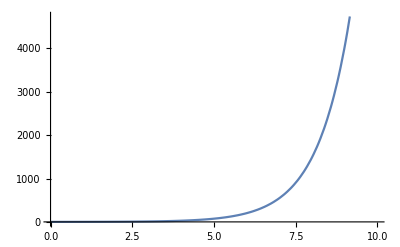

```mathematica
Plot[Sinh[x], {x, 0, 10}]
```

```mathematica
Limit[Sinh[x]/Exp[x], x->Infinity]
```

1/2

```mathematica
((Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep] ==Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep]))/.ep->λ/k1
```

Cosh[k1+2 r T λ-(2 r^2 T^2 λ^2)/k1]==Sinh[k1+2 r T λ-(2 r^2 T^2 λ^2)/k1]

```mathematica
Solve[((Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep] ==Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep]))/.ep->λ/k1, k1]
```

{}

```mathematica
Expand[%]
```

ⅇ^(λ/ep+O[ep]^2) O[ep]^1+ⅇ^(λ/ep+O[ep]^2) Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] (x0+O[ep]^1)+ⅇ^(λ/ep+O[ep]^2) (-x0+O[ep]^1) Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^2]

```mathematica
Manipulate[Plot[{4 T^2 λ^2 σξ^2 (-1+Cosh[√x √(4 r T λ+x)]) a, (-2 T λ (T xh0 λ+(-r x0+xx0) x)+Cosh[√x √(4 r T λ+x)] (2 T^2 xh0 λ^2+2 T (r x0+xx0) λ x+x0 x^2)-√x √(4 r T λ+x) (2 T xx0 λ+x0 x) Sinh[√x √(4 r T λ+x)])},{x, 0, 10}], {T, 0, 5}, {x0, 0, 5}, {xh0, 0, 5}, {xx0, 0, 5}, {λ, 1, 1},{σξ,0,5}, {a, 0, 5}, {r, 1, 10}]
```

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[%126, {K1[tp]}, tp]
```

{(ⅇ^K1[tp] (8 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp) λ^2 σξ^2 K1[tp] (4 r (T-tp) λ+K1[tp]) K1'[tp]-4 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1[tp] (4 r λ-K1'[tp]) K1'[tp]+4 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 (4 r (T-tp) λ+K1[tp]) K1'[tp]^2+8 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp]))) (T-tp)^2 λ^2 σξ^2 √K1[tp] √(4 r (T-tp) λ+K1[tp]) K1'[tp] (K1[tp] (2 r λ-K1'[tp])+2 r (-T+tp) λ K1'[tp])-4 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 √K1[tp] √(4 r (T-tp) λ+K1[tp]) K1'[tp] (K1[tp] (2 r λ-K1'[tp])+2 r (-T+tp) λ K1'[tp]+√K1[tp] √(4 r (T-tp) λ+K1[tp]) K1'[tp])-ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) K1[tp] (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)-ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (4 r (T-tp) λ+K1[tp]) (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)-ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) √K1[tp] √(4 r (T-tp) λ+K1[tp]) (2 r (T-tp) λ+K1[tp]-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)+1/2 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) √K1[tp] √(4 r (T-tp) λ+K1[tp]) (-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2+8 ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])) (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp]))) r (T-tp) λ σg^2 K1[tp] (2 r (T-tp) λ+K1[tp])+4 ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp])) σg^2 K1[tp]^2 (2 r (T-tp) λ+K1[tp])+4 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 √K1[tp] √(4 r (T-tp) λ+K1[tp])+4 (1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])-4 ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp])) σg^2 K1[tp]^(3/2) (2 r (T-tp) λ+K1[tp]) √(4 r (T-tp) λ+K1[tp])-3 (-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp] (4 r (T-tp) λ+K1[tp])+8 ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp]))) (T-tp)^2 λ^2 σξ^2 (2 r (T-tp) λ+K1[tp]) K1'[tp]^2)-4 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1[tp] (4 r (T-tp) λ+K1[tp]) K1''[tp]))/(2 K1[tp]^2 (4 r (T-tp) λ+K1[tp])^2)==0}

```mathematica
Simplify[%]
```

{(2 ⅇ^(K1[tp]-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (T-tp) λ (2 ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])) r σg^2 K1[tp]^3+4 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp)^2 λ^2 σξ^2 K1'[tp]^2-2 (-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) r (T-tp)^2 λ^2 σξ^2 √K1[tp] √(4 r (T-tp) λ+K1[tp]) K1'[tp]^2+(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp]) (r (-1+2 r (T-tp) λ) σg^2+4 r (T-tp) λ^2 σξ^2 K1'[tp]+(-T+tp) λ σξ^2 K1'[tp]^2)-2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp) λ σξ^2 K1[tp] (-4 r λ K1'[tp]+(-1+2 r (T-tp) λ) K1'[tp]^2+4 r (T-tp) λ K1''[tp])+K1[tp]^2 (r (1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-2+8 r (T-tp) λ)) σg^2+4 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 λ σξ^2 K1'[tp]-(-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp) λ σξ^2 K1'[tp]^2-2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp) λ σξ^2 K1''[tp])))/(√K1[tp] (4 r (T-tp) λ+K1[tp]))==0}

```mathematica
FullSimplify[%129]
```

{(ⅇ^K1[tp] (T-tp) λ (r σg^2 K1[tp]^3+4 r (T-tp)^2 λ^2 σξ^2 (-1+Cosh[√K1[tp] √(4 r (T-tp) λ+K1[tp])]) K1'[tp]^2-2 r (T-tp)^2 λ^2 σξ^2 √K1[tp] √(4 r (T-tp) λ+K1[tp]) Sinh[√K1[tp] √(4 r (T-tp) λ+K1[tp])] K1'[tp]^2+K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp]) Sinh[√K1[tp] √(4 r (T-tp) λ+K1[tp])] (r (-1+2 r (T-tp) λ) σg^2+(T-tp) λ σξ^2 (4 r λ-K1'[tp]) K1'[tp])-2 (T-tp) λ σξ^2 (-1+Cosh[√K1[tp] √(4 r (T-tp) λ+K1[tp])]) K1[tp] (-4 r λ K1'[tp]+(-1+2 r (T-tp) λ) K1'[tp]^2+4 r (T-tp) λ K1''[tp])+K1[tp]^2 (r σg^2 (-1+4 r (T-tp) λ+Cosh[√K1[tp] √(4 r (T-tp) λ+K1[tp])])+λ σξ^2 (-1+Cosh[√K1[tp] √(4 r (T-tp) λ+K1[tp])]) (K1'[tp] (4+(-T+tp) K1'[tp])+2 (-T+tp) K1''[tp]))))/(√K1[tp] (4 r (T-tp) λ+K1[tp]))==0}

```mathematica
%/.{K1[tp]->c*tp, K1'[tp]->c, K1''[tp]->0}
```

{1/(√(c tp) (c tp+4 r (T-tp) λ))ⅇ^(c tp) (T-tp) λ (c^3 r tp^3 σg^2+4 c^2 r (T-tp)^2 λ^2 σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])-2 c (T-tp) tp λ (-4 c r λ+c^2 (-1+2 r (T-tp) λ)) σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])+c^2 tp^2 (c (4+c (-T+tp)) λ σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])+r σg^2 (-1+4 r (T-tp) λ+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)]))-2 c^2 r (T-tp)^2 √(c tp) λ^2 √(c tp+4 r (T-tp) λ) σξ^2 Sinh[√(c tp) √(c tp+4 r (T-tp) λ)]+(c tp)^(3/2) √(c tp+4 r (T-tp) λ) (r (-1+2 r (T-tp) λ) σg^2+c (T-tp) λ (-c+4 r λ) σξ^2) Sinh[√(c tp) √(c tp+4 r (T-tp) λ)])==0}

```mathematica
Limit[1/(√(c tp) (c tp+4 r (T-tp) λ))ⅇ^(c tp) (T-tp) λ (c^3 r tp^3 σg^2+4 c^2 r (T-tp)^2 λ^2 σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])-2 c (T-tp) tp λ (-4 c r λ+c^2 (-1+2 r (T-tp) λ)) σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])+c^2 tp^2 (c (4+c (-T+tp)) λ σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])+r σg^2 (-1+4 r (T-tp) λ+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)]))-2 c^2 r (T-tp)^2 √(c tp) λ^2 √(c tp+4 r (T-tp) λ) σξ^2 Sinh[√(c tp) √(c tp+4 r (T-tp) λ)]+(c tp)^(3/2) √(c tp+4 r (T-tp) λ) (r (-1+2 r (T-tp) λ) σg^2+c (T-tp) λ (-c+4 r λ) σξ^2) Sinh[√(c tp) √(c tp+4 r (T-tp) λ)]), T->Infinity]
```

$Aborted

```mathematica
Limit[%134,T->Infinity]
```

{ConditionalExpression[False,(c^3 r tp^3 σg^2|σξ^2|σg^2)∈ℝ&&√(c tp)>0&&r λ>0]}

```mathematica
FullSimplify[%]
```

$Aborted